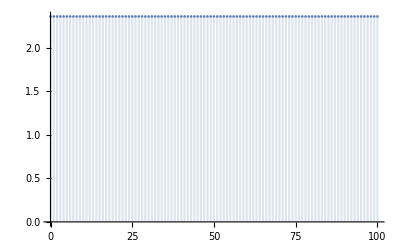

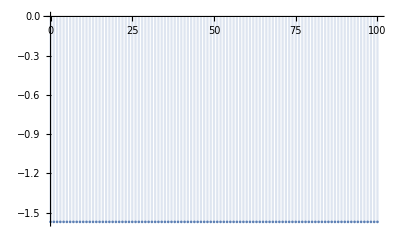

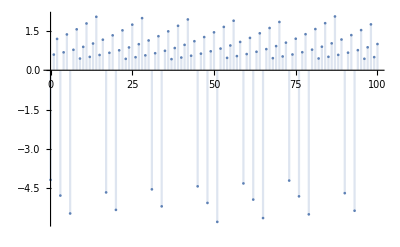

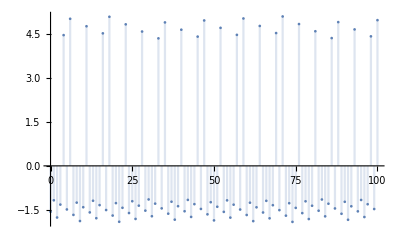

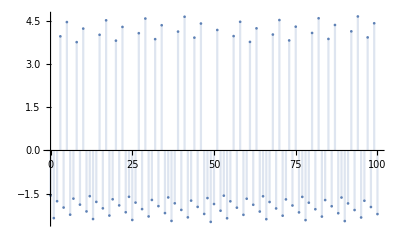

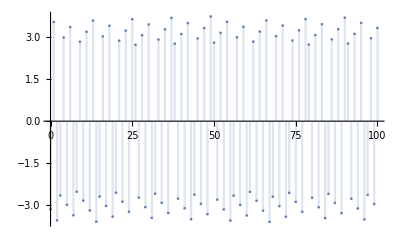

```mathematica
ClearAll["Global`*"];

fnfact[n_, base_]:=n/(base^(Floor[Log[base,n]]+1)-base^Floor[Log[base,n]]);

angle[n_,base_]:=(
 2Pi fnfact[n,base]
);

p[a_,c_,base_,mul_]:=(
DiscretePlot[angle[mul^n*a, base]-angle[mul^n*c,base],{n, 0,100}]
);

p[7,11,2,2]
p[1,5,2,2]
p[1,5,7,2]
p[11,13,2,3]
p[1,5,2,3]
p[5,7,2,3]
```